# Boltzmann Machines

### Create random machine

```mathematica
W=RandomReal[{-100,+100},{8,8}];
Do[W[[i,i]] = 0,{i,8}];
W=W+Wᵀ;
theta=RandomReal[10,8]
```

{4.73071,8.16999,8.41075,5.57371,9.04915,6.38221,8.61176,0.139792}

### Fundamental algorithm

```mathematica
Energy[w_,θ_][s_] := θ . s - ((s . w. s)/2);
```

```mathematica
UpdateState[w_,θ_][s_]:= With[{s2 = MapAt[1-#&, s, RandomInteger[{1,Length[s]}]]},
If[Energy[w,θ][s2]<Energy[w,θ][s],s2,s]]
```

### Utility functions

```mathematica
graycode[n_]:=Map[IntegerDigits[#,2,n]&,Map[BitXor[#,Floor[#/2]]&,Range[0,2^n-1]]]
```

```mathematica
Converge[w_,θ_][state_]:=Nest[UpdateState[w,θ],state,300]
```

```mathematica
FindAttractors[w_,θ_][state_] := Tally[Table[Converge[w,θ][state],{i,40}]]
```

```mathematica
FindBasins[w_,θ_]:={ FindAttractors[w,θ][#],#}&/@graycode[Length[θ]]
```

#### Basins Of Attraction

```mathematica
basins = FindBasins[W, theta];
```

### The Attractors

```mathematica
nbrs[state_]:=Table[ReplacePart[state,i->1-state[[i]]],{i,Length[state]}]
MinimumQ[w_,θ_][state_]:=Min[Map[Energy[w,θ],nbrs[state]]] > Energy[w,θ][state];
AllAttractors[w_,θ_]:= Select[Tuples[{0,1},Length[θ]], MinimumQ[w,θ]];
```

```mathematica
att1=AllAttractors[W,theta];
att=Cases[graycode[8],Alternatives@@att1]
```

{{0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,1}}

### Colouring Scheme for the Hilbert Curve

```mathematica
blend[{x_}, {_}] := x;
blend[a_, b_]:=Blend[a,b]; 
colourmap[w_,θ_][l_]:= Hue[Flatten[Position[att,l]]/Length[att]+0.01]
weightedcolour[l_] := blend[Map[colourmap[W,theta], l[[All,1]]], l[[All,2]]];
```

#### Indexing

```mathematica
Indexpos[k_][{a_,b_}]:={a,k}
PutIndex[lis_]:=Module[{l={}},For [p=1,p<=Length[lis],p++,AppendTo[l,Indexpos[p][lis[[p]]]]];l]
```

### Hilbert Curve : 1-D =>> 2-D map

```mathematica
rot[s_,x_,y_,rx_,ry_]:=Module[ {x1=x,y1=y,tp},

If[ry==0,If[rx==1,x1=s-1-x;y1=s-1-y;];tp=x1;x1=y1;y1=tp;];
{s,x1,y1,rx,ry}
]
d2xy[n_][d_]:=Module[{rx,ry,t=d,x=0,y=0,s},
For[s=1,s<n,s*=2,rx=BitAnd[1,Floor[(t/2)]];ry=BitAnd[1,BitXor[t,rx]];
{s,x,y,rx,ry}=rot[s,x,y,rx,ry];x=x+(s*rx);y=y+(s*ry);t=Floor[t/4];
];
{x,y}
]
```

## Execution:

```mathematica
MapHilbert[l_,n_]:= MapThread[{#1,d2xy[n][#2]}&,Transpose@l]
h={weightedcolour[#1], #2}& @@@ MapHilbert[PutIndex[basins],16];
```

```mathematica
h
```

{{Hue[{0.51}],{1,0}},{Hue[0.0975,1,1],{1,1}},{Hue[0.035,1,1],{0,1}},{Hue[0.11,1,1],{0,2}},{Hue[0.0475,1,1],{0,3}},{Hue[0.0225,1,1],{1,3}},{Hue[0.06,1,1],{1,2}},{Hue[0.1975,1,1],{2,2}},{Hue[0.06,1,1],{2,3}},{Hue[{1.01}],{3,3}},{Hue[{1.01}],{3,2}},{Hue[0.0475,1,1],{3,1}},{Hue[0.11,1,1],{2,1}},{Hue[{1.01}],{2,0}},{Hue[{1.01}],{3,0}},{Hue[0.16,1,1],{4,0}},{Hue[0.06,1,1],{4,1}},{Hue[{1.01}],{5,1}},{Hue[0.035,1,1],{5,0}},{Hue[0.0475,1,1],{6,0}},{Hue[0.0225,1,1],{7,0}},{Hue[0.0225,1,1],{7,1}},{Hue[{1.01}],{6,1}},{Hue[0.035,1,1],{6,2}},{Hue[{1.01}],{7,2}},{Hue[0.0225,1,1],{7,3}},{Hue[{1.01}],{6,3}},{Hue[{1.01}],{5,3}},{Hue[{1.01}],{5,2}},{Hue[0.035,1,1],{4,2}},{Hue[0.0475,1,1],{4,3}},{Hue[0.1225,1,1],{4,4}},{Hue[{1.01}],{4,5}},{Hue[{1.01}],{5,5}},{Hue[{1.01}],{5,4}},{Hue[{1.01}],{6,4}},{Hue[{1.01}],{7,4}},{Hue[{1.01}],{7,5}},{Hue[{1.01}],{6,5}},{Hue[{1.01}],{6,6}},{Hue[0.0225,1,1],{7,6}},{Hue[{1.01}],{7,7}},{Hue[0.0225,1,1],{6,7}},{Hue[{1.01}],{5,7}},{Hue[0.0225,1,1],{5,6}},{Hue[{1.01}],{4,6}},{Hue[{1.01}],{4,7}},{Hue[0.0225,1,1],{3,7}},{Hue[0.0975,1,1],{2,7}},{Hue[{1.01}],{2,6}},{Hue[{1.01}],{3,6}},{Hue[{1.01}],{3,5}},{Hue[0.0225,1,1],{3,4}},{Hue[0.0225,1,1],{2,4}},{Hue[{1.01}],{2,5}},{Hue[0.035,1,1],{1,5}},{Hue[0.0475,1,1],{1,4}},{Hue[{1.01}],{0,4}},{Hue[{1.01}],{0,5}},{Hue[0.0475,1,1],{0,6}},{Hue[0.06,1,1],{1,6}},{Hue[0.035,1,1],{1,7}},{Hue[{1.01}],{0,7}},{Hue[0.085,1,1],{0,8}},{Hue[0.0225,1,1],{0,9}},{Hue[{1.01}],{1,9}},{Hue[{1.01}],{1,8}},{Hue[{1.01}],{2,8}},{Hue[0.035,1,1],{3,8}},{Hue[{1.01}],{3,9}},{Hue[{1.01}],{2,9}},{Hue[0.0225,1,1],{2,10}},{Hue[0.0225,1,1],{3,10}},{Hue[{1.01}],{3,11}},{Hue[{1.01}],{2,11}},{Hue[{1.01}],{1,11}},{Hue[{1.01}],{1,10}},{Hue[{1.01}],{0,10}},{Hue[{1.01}],{0,11}},{Hue[{1.01}],{0,12}},{Hue[{1.01}],{1,12}},{Hue[{1.01}],{1,13}},{Hue[{1.01}],{0,13}},{Hue[{1.01}],{0,14}},{Hue[{1.01}],{0,15}},{Hue[{1.01}],{1,15}},{Hue[{1.01}],{1,14}},{Hue[{1.01}],{2,14}},{Hue[{1.01}],{2,15}},{Hue[{1.01}],{3,15}},{Hue[{1.01}],{3,14}},{Hue[{1.01}],{3,13}},{Hue[{1.01}],{2,13}},{Hue[{1.01}],{2,12}},{Hue[{1.01}],{3,12}},{Hue[{1.01}],{4,12}},{Hue[{1.01}],{5,12}},{Hue[{1.01}],{5,13}},{Hue[{1.01}],{4,13}},{Hue[{1.01}],{4,14}},{Hue[{1.01}],{4,15}},{Hue[{1.01}],{5,15}},{Hue[{1.01}],{5,14}},{Hue[{1.01}],{6,14}},{Hue[{1.01}],{6,15}},{Hue[{1.01}],{7,15}},{Hue[{1.01}],{7,14}},{Hue[{1.01}],{7,13}},{Hue[{1.01}],{6,13}},{Hue[{1.01}],{6,12}},{Hue[{1.01}],{7,12}},{Hue[{1.01}],{7,11}},{Hue[{1.01}],{7,10}},{Hue[{1.01}],{6,10}},{Hue[{1.01}],{6,11}},{Hue[{1.01}],{5,11}},{Hue[{1.01}],{4,11}},{Hue[{1.01}],{4,10}},{Hue[{1.01}],{5,10}},{Hue[{1.01}],{5,9}},{Hue[0.0225,1,1],{4,9}},{Hue[{1.01}],{4,8}},{Hue[{1.01}],{5,8}},{Hue[0.035,1,1],{6,8}},{Hue[{1.01}],{6,9}},{Hue[{1.01}],{7,9}},{Hue[{1.01}],{7,8}},{Hue[0.11,1,1],{8,8}},{Hue[{1.01}],{8,9}},{Hue[{1.01}],{9,9}},{Hue[{1.01}],{9,8}},{Hue[{1.01}],{10,8}},{Hue[{1.01}],{11,8}},{Hue[{1.01}],{11,9}},{Hue[{1.01}],{10,9}},{Hue[{1.01}],{10,10}},{Hue[{1.01}],{11,10}},{Hue[{1.01}],{11,11}},{Hue[{1.01}],{10,11}},{Hue[{1.01}],{9,11}},{Hue[{1.01}],{9,10}},{Hue[{1.01}],{8,10}},{Hue[{1.01}],{8,11}},{Hue[{1.01}],{8,12}},{Hue[{1.01}],{9,12}},{Hue[{1.01}],{9,13}},{Hue[{1.01}],{8,13}},{Hue[{1.01}],{8,14}},{Hue[{1.01}],{8,15}},{Hue[{1.01}],{9,15}},{Hue[{1.01}],{9,14}},{Hue[{1.01}],{10,14}},{Hue[{1.01}],{10,15}},{Hue[{1.01}],{11,15}},{Hue[{1.01}],{11,14}},{Hue[{1.01}],{11,13}},{Hue[{1.01}],{10,13}},{Hue[{1.01}],{10,12}},{Hue[{1.01}],{11,12}},{Hue[{1.01}],{12,12}},{Hue[{1.01}],{13,12}},{Hue[{1.01}],{13,13}},{Hue[{1.01}],{12,13}},{Hue[{1.01}],{12,14}},{Hue[{1.01}],{12,15}},{Hue[{1.01}],{13,15}},{Hue[{1.01}],{13,14}},{Hue[{1.01}],{14,14}},{Hue[{1.01}],{14,15}},{Hue[{1.01}],{15,15}},{Hue[{1.01}],{15,14}},{Hue[{1.01}],{15,13}},{Hue[{1.01}],{14,13}},{Hue[{1.01}],{14,12}},{Hue[{1.01}],{15,12}},{Hue[{1.01}],{15,11}},{Hue[{1.01}],{15,10}},{Hue[{1.01}],{14,10}},{Hue[{1.01}],{14,11}},{Hue[{1.01}],{13,11}},{Hue[{1.01}],{12,11}},{Hue[{1.01}],{12,10}},{Hue[{1.01}],{13,10}},{Hue[{1.01}],{13,9}},{Hue[{1.01}],{12,9}},{Hue[{1.01}],{12,8}},{Hue[{1.01}],{13,8}},{Hue[{1.01}],{14,8}},{Hue[{1.01}],{14,9}},{Hue[{1.01}],{15,9}},{Hue[{1.01}],{15,8}},{Hue[{1.01}],{15,7}},{Hue[{1.01}],{14,7}},{Hue[{1.01}],{14,6}},{Hue[{1.01}],{15,6}},{Hue[{1.01}],{15,5}},{Hue[{1.01}],{15,4}},{Hue[{1.01}],{14,4}},{Hue[{1.01}],{14,5}},{Hue[{1.01}],{13,5}},{Hue[{1.01}],{13,4}},{Hue[{1.01}],{12,4}},{Hue[{1.01}],{12,5}},{Hue[{1.01}],{12,6}},{Hue[{1.01}],{13,6}},{Hue[{1.01}],{13,7}},{Hue[{1.01}],{12,7}},{Hue[{1.01}],{11,7}},{Hue[{1.01}],{11,6}},{Hue[{1.01}],{10,6}},{Hue[{1.01}],{10,7}},{Hue[{1.01}],{9,7}},{Hue[{1.01}],{8,7}},{Hue[{1.01}],{8,6}},{Hue[{1.01}],{9,6}},{Hue[{1.01}],{9,5}},{Hue[{1.01}],{8,5}},{Hue[{1.01}],{8,4}},{Hue[{1.01}],{9,4}},{Hue[{1.01}],{10,4}},{Hue[{1.01}],{10,5}},{Hue[{1.01}],{11,5}},{Hue[{1.01}],{11,4}},{Hue[{1.01}],{11,3}},{Hue[{1.01}],{11,2}},{Hue[{1.01}],{10,2}},{Hue[{1.01}],{10,3}},{Hue[{1.01}],{9,3}},{Hue[{1.01}],{8,3}},{Hue[{1.01}],{8,2}},{Hue[{1.01}],{9,2}},{Hue[{1.01}],{9,1}},{Hue[{1.01}],{8,1}},{Hue[{1.01}],{8,0}},{Hue[{1.01}],{9,0}},{Hue[{1.01}],{10,0}},{Hue[{1.01}],{10,1}},{Hue[{1.01}],{11,1}},{Hue[{1.01}],{11,0}},{Hue[{1.01}],{12,0}},{Hue[{1.01}],{13,0}},{Hue[{1.01}],{13,1}},{Hue[{1.01}],{12,1}},{Hue[{1.01}],{12,2}},{Hue[{1.01}],{12,3}},{Hue[{1.01}],{13,3}},{Hue[{1.01}],{13,2}},{Hue[{1.01}],{14,2}},{Hue[{1.01}],{14,3}},{Hue[{1.01}],{15,3}},{Hue[{1.01}],{15,2}},{Hue[{1.01}],{15,1}},{Hue[{1.01}],{14,1}},{Hue[{1.01}],{14,0}},{Hue[{1.01}],{15,0}},{Hue[0.035,1,1],{0,0}}}

```mathematica
arr=ConstantArray[0,{16,16}];
setarr[col_, {p1_,p2_}]:=arr[[1+p1,1+p2]]=col;
setarr @@@ h;
```

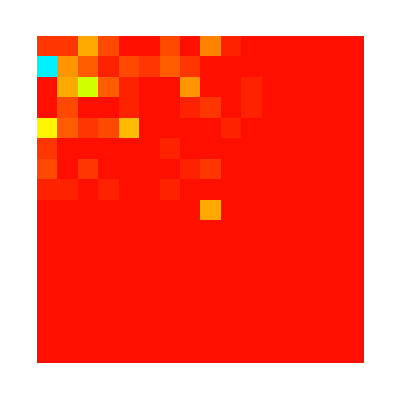

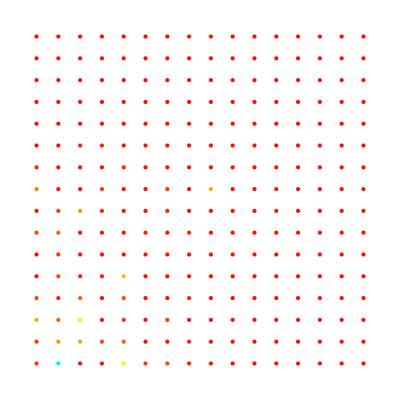

```mathematica
ArrayPlot[arr]

Graphics[{PointSize[Large],Style[Point[#2],#1]&@@@h}]
```